# Dark Matter Freeze-out

The following notebook implements the simplified Ricatti equation for dark matter freezeout and computes the residual density, as a function of the annihilation cross section.

Just for completeness, the Ricatti equation for DM freezeout, derived from the Boltzmann equation is

dY/dx= -λ/x^2(Y^2 - (Y^2)_eq)

where Y = n/T^3, x=M/T is our time variable and λ characterizes the annihilation cross-section. See the textbook/class notes for more details on the derivation of this equation.

## Equilibrium

To start, we need to calculate Y_eq as a function of x. We do this by integrating the Fermi-Dirac distribution using the code below. One numerical note - as x gets large, Y_eq-> 0, but the numerical integral starts to complain about accuracy (hard to compute a number incredibly close to zero). To avoid these complaints, we just set it to zero after a particular value (100 below).

Another Mathematica specific note : Mathematica can sometimes try to symbolically process equations, even when you want something purely numerical. The NumberQ annotation here forces it to only evaluate when given a numerical value.

```mathematica
ClearAll[yeq];
yeq[x_?NumberQ]:=1/(2 π^2)NIntegrate[t^2/(Exp[Sqrt[t^2+x^2]]+1),{t,0,Infinity}]/;x<=100
yeq[x_?NumberQ]:=0/;x>100
```

Let us see what we get at very high temperatures (x=0)

```mathematica
yeq[0.0]
```

0.0913454

Let us also verify (as we might expect) that the equilibrium number is vanishingly small when you get to temperatures close to the place where we stop the actual evaluation.

```mathematica
yeq[50]
```

4.49351×10^-21

```mathematica
yeq[100]
```

2.40649×10^-42

Ok, that is all nice and small.

## Boltzmann Equation

Here is a function that solves the full Boltzmann equation for different values of λ. Note that you need to specify both the differential equation and the initial condition, which is set by the equilibrium value. Start just past x=0 to avoid a divide by zero issue.

```mathematica
ClearAll[solveDM, xstart, xend];
xstart=0.001;
xend=1000;
solveDM[λ_]:=NDSolveValue[{y'[x]==-λ/x^2(y[x]^2-yeq[x]^2),y[xstart]==yeq[xstart]},y,{x,xstart,xend}]
```

Generate some solutions

```mathematica
sol7=solveDM[10^7]
sol5=solveDM[10^5]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

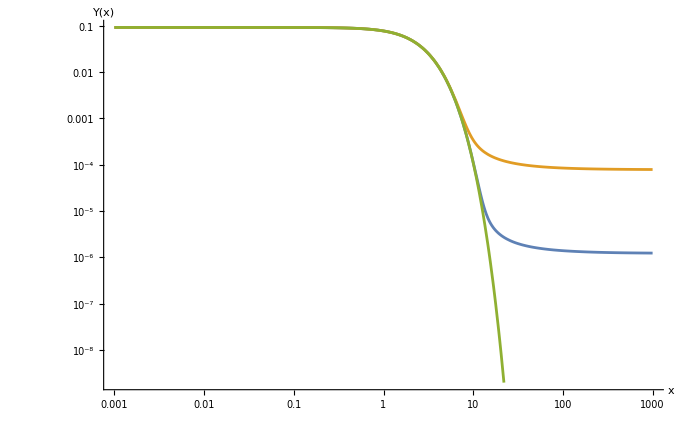

```mathematica
LogLogPlot[{sol7[x], sol5[x], yeq[x]},{x,xstart, xend}, ImageSize->Large, AxesLabel->{"x","Y(x)"},
LabelStyle->Large]
```